## Step 1. Load the bistatic scattering program- IEMM

```mathematica
Off[General::"spell1"];(Off[General::"spell"];)
BeginPackage["IEMM`"];
IEMM::"usage"="Calculates Bistatic Single surface scattering";
Begin["`private`"];
IEMM[fr_,sig_,corr_,theta_,ths_,phs_,er_,sp_,xx_]:=Module[{},
k=(2.0 π fr)/30.0;phi=0.0;σ=sig;L=corr;μr=1;thetas=ths;
ks=k sig;kL=k*corr;

s=N[Sin[(theta+0.01) Degree]];
cs=N[Cos[(theta+0.01) Degree]];
sf=N[Sin[phi Degree]];
cf=N[Cos[phi Degree]];

ss=N[Sin[ths Degree]];s2=s*s;
css=N[Cos[ths Degree]];
cfs=N[Cos[phs Degree]];
sfs=N[Sin[phs Degree]];

  kx=N[k s cf];       ky=N[k s sf];      kz=N[k cs];
ksx=N[k ss cfs];ksy=N[k ss sfs];ksz=N[k css];

rt=√(er-s^2);Rvi=N[(er cs-rt)/(er cs+rt)];Rhi=N[(cs-rt)/(cs+rt)];


wvnb=k √((ss cfs-s cf)^2+(ss sfs- s sf)^2);
TS=1;error=10^8;While[error>1/10^8,TS=TS+1;error=((ks^2 (cs+css)^2)^TS)/(TS!);];
spctrm=Switch[sp,
			           1,Do[ w[n]=N[L^2/n^2 (1+((wvnb L)/n)^2)^-1.5],{n,1,TS,1}],
				2,Do[ w[n]=N[L^2/(2 n) Exp[-(wvnb L)^2/(4 n)]],{n,1,TS,1}],
3,Do[ w[n]=If[wvnb==0,L^2/(3 n-2),N[(L^2 (wvnb L)^(xx n-1) BesselK[-xx n+1,wvnb L])/(2^(xx n-1) Gamma[xx n])]],{n,1,TS,1}],	
4,Do[ w[n]=  L^2/n^(2/xx)*NIntegrate[Exp[-(Abs[z])^xx]*BesselJ[0,z*wvnb L*(1/n^(1/xx))]*z,{z,0,9}],{n,1,TS,1}],
5,Do[ w[n]=N[∑_(m=0)^(TS+5) L^2 n^m/(m!) (xx/(n xx+m L))^(m+2)  Gamma[2+m] Hypergeometric2F1[(2+m)/2,(3+m)/2,1,-((xx  wvnb L)/(n xx+m L))^2]],{n,1,TS,1}]   ];

(*Compute R-transition*)
Rv0=N[(er -√er)/(er +√er)];Rh0=-Rv0;	Ft=8  Rv0^2 s*s( (cs+√(er-s^2))/(cs √(er-s^2)));
	
St=(0.25*Abs[Ft]^2 ∑_(n=1)^TS (ks cs)^(2 n)/(n!)w[n])/(∑_(n=1)^TS (ks cs)^(2 n)/(n!)Abs[Ft/2+2^(n+1)Rv0/cs Exp[-(ks cs)^2]]^2 w[n]);


(*there is really no difference between Stv and Sth !  St0= Stv when n=1 and ks-> 0. We drop v or h *)


(*S0=(0.25 ks cs Abs[Fvv]^2 w[n])/(ks cs Abs[Fvv/2+2^(n+1)Rv0/cs Exp[-(ks cs)^2]]^2 w[n])=(0.25 Abs[Fvv]^2)/Abs[Fvv/2+4 Rv0/cs]^2=Abs[Fvv]^2/Abs[Fvv+8 Rv0/cs]^2 has no polarization dependence*)

St0=1/Abs[1+8 Rv0/(cs *Ft)]^2;
Tf=1-St/St0;

Rtv=Rvi +(Rv0-Rvi)Tf;
Rth=Rhi +(Rh0-Rhi)Tf;

(*Rtv, Rth are needed for frequency behavior calculation
		
	A=(cs+Zx*s);
	B=er*(1+Zx^2+Zy^2);
	CC=s^2-2*Zx*s*cs+Zx^2*cs^2+Zy^2;
	
	Rh=(A-√(B-CC))/(A+√(B-CC)); Rv=(er*A-√(B-CC))/(er*A+√(B-CC));
	
σx=1.1*sig/L;σy=σx;
	pd=Exp[-Zx^2/(2*σx^2)-Zy^2/(2*σy^2)];
	Ra=1/(2*π*σx*σy)*NIntegrate[{Rv*pd,Rh*pd},{Zx,-3*σx,0,3*σx},{Zy,-3*σy,0,3*σy}];
			
		
 fvv=((2  Ra[[1]]) (s ss-(1+cs css) cfs))/(cs+css);fhh=-((2 Ra[[2]]) (s ss-(1+cs css) cfs))/(cs+css);*)
	(* Average reflection coefficients, Ra[[1]] and Ra[[2]], are to correct scattering near the Brewster angle*)

fvv=N[1/(cs+css)( (2 Rtv) (s ss-(cs css+1) cfs))]; 
fhh=N[-1/(cs+css)((2 Rth) (s ss-(cs css+1) cfs))];



(*There are 4 F-coefficients:up-down (ud)and incident-scatter (is) *)
		 F[ud_,is_]:=Module[{vv,hh,c11,c21,c31,c41,c51,c61,c12,c22,c32,c42,c52,c62,q,qt},
				If[is==1,{
Gqi=ud kz; (* Gqi will switch to Gqti, when Ci1 changes to Ci2. This applies to C2i, C3i, C5i*)  Gqti=ud k √(er-s^2);qi=ud kz;

c11=k cfs (ksz-qi);
c21= cs (cfs(k^2 s cf (ss cfs-s cf)+  Gqi (k css-qi))+ k^2 cf s ss  sfs^2);c31= k s(s cf cfs(k css-qi) -Gqi (cfs (ss cfs-s cf) + ss sfs^2));
c41=k cs (cfs  css (k css-qi)+k ss(ss cfs-s cf));
c51=Gqi (cfs css (qi-k css)-k ss(ss cfs-s cf));

c12=k cfs  (ksz-qi);
c22=cs (cfs(k^2 s cf(ss cfs-s cf)+  Gqti (k css-qi))+ k^2 cf s ss  sfs^2);
c32= k s(s cf cfs(k css-qi) -Gqti (cfs (ss cfs-s cf) - ss sfs^2));
c42=k cs (cfs  css (k css-qi)+k ss(ss cfs-s cf));
c52=Gqti (cfs css (qi-k css)-k ss(ss cfs-s cf));

}
						];
				
        If[is==2,{
Gqs=ud ksz; qs=ud ksz;Gqts=ud k √(er-ss^2);
						c11=cfs k (kz+qs);
						c21=Gqs (cfs (cs (k cs+qs)-k s(ss cfs-s cf))-k s ss sfs^2);
						c31= k ss(k cs(ss cfs-s cf)+ s(kz+qs) );
						c41=k css(cfs(cs (kz+qs)-k s(ss cfs-s cf) )-k s ss sfs^2);
						c51=-css ( k^2 ss  (ss cfs-s cf)+Gqs cfs(kz+qs));
						
						c12=cfs k (kz+qs);
						c22=Gqts (cfs (cs (kz+qs)-k s(ss cfs-s cf))-k s ss sfs^2);
						c32= k ss(k cs(ss cfs-s cf)+ s(kz+qs) );
						c42=k css(cfs(cs (kz+qs)-k s(ss cfs-s cf) )-k s ss sfs^2);
						c52=-css ( k^2 ss  (ss cfs-s cf)+Gqts cfs(kz+qs));
					}
						]; 
q=kz;qt=k √(er-s^2);
vv=(1+Rvi) (-1/q((1-Rvi)c11)+((1+Rvi)c12)/qt)+
						(1-Rvi) (((1-Rvi)c21)/q-((1+Rvi)c22)/qt)+
						(1+Rvi) (((1-Rvi)c31)/q-((1+Rvi)c32)/(er qt))+
						(1-Rvi)(((1+Rvi)c41)/q-1/qt(er(1-Rvi)c42))+
						(1+Rvi) (((1+Rvi)c51)/q-((1-Rvi)c52)/qt);
hh= (1+Rhi) (((1-Rhi)c11)/q-1/qt(er (1+Rhi)c12))-
						(1-Rhi) (((1-Rhi)c21)/q-((1+Rhi)c22)/qt)-
						(1+Rhi) (((1-Rhi)c31)/q-((1+Rhi)c32)/qt)-
						(1-Rhi) (((1+Rhi)c41)/q-((1-Rhi)c42)/qt)-
						(1+Rhi) (((1+Rhi)c51)/q-((1-Rhi)c52)/qt);
Return[{vv,hh}];
];

Fvvupi=F[+1,1]⟦1⟧;Fhhupi=F[+1,1]⟦2⟧;
Fvvdni=F[-1,1]⟦1⟧;Fhhdni=F[-1,1]⟦2⟧;
Fvvups=F[+1,2]⟦1⟧;Fhhups=F[+1,2]⟦2⟧;
Fvvdns=F[-1,2]⟦1⟧;Fhhdns=F[-1,2]⟦2⟧;
		
aav=1/2 k^2 Abs[fvv]^2 Exp[-ks^2 (cs+css)^2] ∑_(n=1)^TS 1/(n!)((ks^2 (cs+css)^2)^n w[n]);
aah=1/2 k^2 Abs[fhh]^2 Exp[-ks^2 (cs+css)^2] ∑_(n=1)^TS 1/(n!)((ks^2 (cs+css)^2)^n w[n]);
kv=10 Log[10,N[aav]];
kh=10 Log[10,N[aah]];
qi=k cs;qs=k css;
(*Do[Ivv[n]=(kz+ksz)^n fvv Exp[-σ^2kz ksz]+
					1/4(Fvvupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fvvdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fvvups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fvvdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]),{n,1,TS,1}];
	
		
Do[Ihh[n]=(kz+ksz)^n fhh Exp[-σ^2kz ksz]+
					1/4(Fhhupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fhhdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fhhups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fhhdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]),{n,1,TS,1}];*)
Ivv=(kz+ksz)^n fvv Exp[-σ^2 kz ksz]+
					1/4(Fvvupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fvvdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fvvups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fvvdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]);
Ihh=(kz+ksz)^n fhh Exp[-σ^2 kz ksz]+
					1/4(Fhhupi (ksz-qi)^(n-1)Exp[-σ^2(qi^2-qi(ksz-kz))]+
								Fhhdni (ksz+qi)^(n-1)Exp[-σ^2(qi^2+qi(ksz-kz))]+
								Fhhups (kz+qs)^(n-1)Exp[-σ^2(qs^2-qs(ksz-kz))]+
								Fhhdns (kz-qs)^(n-1)Exp[-σ^2(qs^2+qs(ksz-kz))]);

(*ct=N[Cot[theta Degree]];
cts=N[Cot[thetas Degree]];
rslp=Switch[sp,
						1,√1 sig/L,
						2,√2 sig/L,
						3,If[xx==1.5,√3 sig/L,0],
						4,√1 sig/L,
						5,√2 sig/(√(xx* L))];
If[UnsameQ[rslp,0],
ctorslp=ct/(√2 rslp);
ctsorslp=cts/(√2 rslp);
shadf=1/2(1/(√π ctorslp)Exp[-ctorslp^2]-Erfc[ctorslp]);
shadfs=1/2(1/(√π ctsorslp)Exp[-ctsorslp^2]-Erfc[ctsorslp]);
ShdwS=N[1/(1+shadf+shadfs)];
ShdwS=1;
Print["Warning: RMS surface slope not available. Shadowing not used."]]; *)
ShdwS=1;
iemmvv=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[Ivv]^2 w[n]/(n!);
iemmhh=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[Ihh]^2 w[n]/(n!);
ssv=10 Log[10,N[iemmvv]];
ssh=10 Log[10,N[iemmhh]];
(*Compute the old IEM*)
sq=√(μr er-s^2);sqs=√(μr er-ss^2);rcs=(css sq)/(cs sqs);
Fvv=((μr er-s^2-er cs^2)(1+Rvi)^2)/((er cs)^2 css)s(ss-s cfs);Fhh=-((μr er-s^2-μr cs^2)(1+Rhi)^2)/((μr cs)^2 css)s(ss-s cfs);
Fvs=(1-Rvi^2)((1/rcs-1)css cfs +1/cs((1-rcs)(cfs-s ss))+1/sq((er-rcs) ss(s-ss cfs)));
Fhs=-(1-Rhi^2)((1/rcs-1)css cfs +1/cs((1-rcs)(cfs-s ss))+1/sq((μr-rcs) ss(s-ss cfs)));
oIvv=(kz+ksz)^n fvv Exp[-σ^2 kz ksz]+(ksz^n Fvv+kz^n Fvs)/2;
oIhh=(kz+ksz)^n fhh Exp[-σ^2 kz ksz]+(ksz^n Fhh+kz^n Fhs)/2;
iemvv=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[oIvv]^2 w[n]/(n!);
iemhh=ShdwS k^2/2 Exp[-σ^2(kz^2+ksz^2)]∑_(n=1)^TS σ^(2n)Abs[oIhh]^2 w[n]/(n!);

sov=10 Log[10,N[iemvv]];
soh=10 Log[10,N[iemhh]];

Return[{ths,iemmvv,iemmhh,sov,soh}];]
End[];EndPackage[]
```

```mathematica
(*IIEMB[fr_,sig_,corr_,theta_,ths_,phs_,er_,sp_,xx_]*)
```

```mathematica
Do[otp=IEMM[4.775,0.2,1.0,theta,theta,180,62,2,1.5];Print[otp], {theta, 10,40,10}];
```

{10,0.087263,0.0788899,-10.5796,-11.0434}

{20,0.0924912,0.0625237,-10.2994,-12.0932}

{30,0.0984641,0.0422832,-10.0037,-13.8592}

{40,0.101758,0.0241673,-9.853,-16.3879}

```mathematica
(1) This is the Rayleigh layer model.It consists of a top surface scattering term,a bottom surface scattering term,a layer volume scattering term and an interaction term.(2) Exact calculation should use the real angle of transmision given in the program below.er=relative complex dielectric constant of the layer;
erb=relative complex dielectric constant of the half-space below the layer;
```

## Step 2. Load graphics package

```mathematica
Needs["Graphics`MultipleListPlot`"];
sym1=PlotSymbol[Diamond,3];
sym2=PlotSymbol[Triangle,5];
sym3=PlotSymbol[Star,2];
sym4=PlotSymbol[Box,3];
```

## Step 3. Load the Rayleigh Layer Scattering Program (1) This is the Rayleigh layer model. It consists of a top surface scattering term, a bottom surface scattering term, a layer volume scattering term and an interaction term. (2) Exact calculation should use the real angle of transmision given in the program below. er = relative complex dielectric constant of the layer; erb=relative complex dielectric constant of the half-space below the layer;

```mathematica
Off[General::"spell1"];Off[General::"spell"];
BeginPackage["Rlay`",{"IEMM`"}];
Rlay::"usage"="Calculates Layer volume-surf scattering and interaction";
Begin["`private`"];
Rlay[fr_,al_,tau_,theta_,thetas_,phs_,er_,erb_,sig1_,sig2_,L1_,L2_,sp_]:=Module[{},
	k=(2.0 Pi fr)/30.0;kl=k √Re[er];
	
		cs=N[Cos[theta Degree]];
		s=N[Sin[theta Degree]];
		s2=s^2;
		cfs=N[Cos[phs Degree]];
		sfs=N[Sin[phs Degree]];
		css=N[Cos[thetas Degree]];
		ss=N[Sin[thetas Degree]];
		ss2=ss^2;
(* Calculations of sine and cosine using real-thetat and real-thetao*)
alf=Im[√er]//N; be=Re[√er]; p=2 alf* be; q=be^2-alf^2-s2;qs=be^2-alf^2-ss2;
tant=1.414 s/√(q+√(p^2+q^2)); thetat=ArcTan[tant]*180/π; st=Sin[thetat Degree]//N;cst=√(1-st^2);
tano=1.414 ss/√(q+√(p^2+qs^2)); thetao=ArcTan[tano]*180/π; so=Sin[thetao Degree]//N;cso=√(1-so^2);
  
(*Top boundary & bottom reflectivity & transmissivity*)
		rt=√(er-s^2);rvi=N[(er cs-rt)/(er cs+rt)];rhi=N[(cs-rt)/(cs+rt)];Rv=Abs[rvi]^2;Rh=Abs[rhi]^2;
	rts=√(er-ss^2);rvs=N[(er css-rts)/(er css+rts)];rhs=N[(css-rts)/(css+rts)];Rvs=Abs[rvs]^2;Rhs=Abs[rhs]^2;

rtbt=√(erb/er-st^2);rvt=N[((erb/er) cst-rtbt)/((erb/er) cst+rtbt)];rht=N[(cst-rtbt)/(cst+rtbt)];Rvt=Abs[rvt]^2;Rht=Abs[rht]^2;
rtbo=√(erb/er-so^2);rvo=N[((erb/er) cso-rtbo)/((erb/er) cso+rtbo)];rho=N[(cso-rtbo)/(cso+rtbo)];Rvo=Abs[rvo]^2;Rho=Abs[rho]^2;
Tv=1-Rv; Th=1-Rh;
Tvs=1-Rvs; Ths=1-Rhs;

(*Rayleigh Phase functions and the volume scattering terms. Due to difference in definition in Chandrasekar where phs =0 means the TR are together and phs=180 means TR are 180 apart, to use spherical coordinate in defining Phs, we need to add 180 to phs*)

phh=0.75(1+Cos[2 phs Degree]);
pvv=0.75(2  st^2 so^2+cst^2 cso^2(1+Cos[2 phs Degree])+4 cst cso st so Cos[( phs+180) Degree]);
pvvf=0.75(2  st^2 so^2+cst^2 cso^2(1+Cos[2*0 Degree])-4 cst cso st so );

volvv=css cst Tv Tvs al (1-Exp[-(tau(cso+cst))/(cso cst)])pvv/(cso+cst);
volhh=css cst Th Ths al (1-Exp[-(tau(cso+cst))/(cso cst)])phh/(cso+cst);

(*Interaction terms*)
(*注意在计算下表面相干反射时，波数用的媒质中的波数kl而非k，这考虑了媒质介电常数不同于空气的情况，这是非常正确的，因为等效粗糙度会因为介电常数变化而变为（本质是因为波长发生变化），但遗憾的是这里并没有考虑介电常数使得下表面非相干散射IEMM的等效粗糙度也发生了变化*)
If[cso≠cst,
invv=css  Tv  Tvs al((Exp[-tau/cso]-Exp[-tau/cst])/(cso-cst))Exp[-kl^2 sig2^2(cso+cst)^2]pvvf(cso Rvo Exp[-tau/cso]+cst Rvt Exp[-tau/cst]),invv=2 cs Tv^2 al (tau/cst)(Exp[-kl^2 sig2^2(cso+cst)^2] Rvt) pvvf  Exp[-2tau/cst]];

If[cso≠cst,
inhh=css  Th  Ths al((Exp[-tau/cso]-Exp[-tau/cst])/(cso-cst))Exp[-kl^2 sig2^2(cso+cst)^2]phh(cso Rho Exp[-tau/cso]+cst Rht Exp[-tau/cst]),inhh=2 cs Th^2 al (tau/cst)(Exp[-kl^2 sig2^2(cso+cst)^2] Rht) phh Exp[-2tau/cst]];

(*Calculate surface scattering from TOP & BOTTOM boundaries. Call IEMM*)

stop=IEMM[fr,sig1,L1,theta,thetas,phs,er,1,1.5];
stopv=stop[[2]];
stoph=stop[[3]];
  ebr=Re[erb/er];
sbot=IEMM[fr,sig2,L2,thetat,thetao,phs,ebr,1,1.5];
cov=css  Tv Tvs Exp[-tau(1/cso+1/cst)]/cst;
coh=css  Th Ths Exp[-tau(1/cso+1/cst)]/cst;
sbotv=cov*sbot[[2]];
sboth=coh*sbot[[3]];

ssv=volvv+invv+stopv+sbotv;(*Print[{stopv, sbotv}];*)
ssh=volhh+inhh+stoph+sboth;
Rlvv=10.0Log[10.,ssv];vv=10.0Log[10.,volvv];vint=10.0Log[10.,invv];stvv=10.0Log[10.,stopv];sbvv=10.0Log[10.,sbotv];
Rlhh=10.0Log[10.,ssh];hh=10.0Log[10.,volhh];hint=10.0Log[10.,inhh];sthh=10.0Log[10.,stoph];sbhh=10.0Log[10.,sboth];

Return[{thetas,Rlvv,Rlhh,vv, hh, vint,hint,stvv,sthh,sbvv,sbhh, cov,coh}];];
End[];EndPackage[];
```

Rlay::shdw: 符号 Rlay 出现在多个上下文 {Rlay`,Global`} 中；上下文 Rlay` 中的定义可能遮蔽或者被其他定义遮蔽.

```mathematica
fr=10;  al=0.42;tau=0.75; phs=180;
theta=thetas;er=2.1-I 0.002;erb=2.65-I 0.008; sig1=.25;sig2=0.39; L1=5.79; L2=3.4;sp=1;

start=10.01;end=70.01;step=5;

outp=Table[Rlay[fr,al,tau,theta,thetas,phs,er,erb/er,sig1,sig2,L1,L2,sp],{thetas,start,end,step}];
vv=Map[{#[[1]],#[[2]]}&,outp];
hh=Map[{#[[1]],#[[3]]}&,outp];
vov=Map[{#[[1]],#[[4]]}&,outp];
voh=Map[{#[[1]],#[[5]]}&,outp];
inv=Map[{#[[1]],#[[6]]}&,outp];
inh=Map[{#[[1]],#[[7]]}&,outp];
stv=Map[{#[[1]],#[[8]]}&,outp];
sth=Map[{#[[1]],#[[9]]}&,outp];
sbv=Map[{#[[1]],#[[10]]}&,outp];
sbh=Map[{#[[1]],#[[11]]}&,outp];
cov=Map[{#[[1]],#[[12]]}&,outp];
coh=Map[{#[[1]],#[[13]]}&,outp];

Needs["Statistics`DataManipulation`"];


Print[TableForm[{vv},TableHeadings->{{"VV σ^0"},{"Layer"}}]];
Print[TableForm[{hh},TableHeadings->{{"HH σ^0"},{"Layer"}}]];
Null
```

| Layer |  |  |  |  |  |  |  |  |  |  |  | 
VV σ^0 | 10.01
-4.44075 | 15.01
-5.56918 | 20.01
-6.05774 | 25.01
-6.34727 | 30.01
-6.57546 | 35.01
-6.7962 | 40.01
-7.03768 | 45.01
-7.32111 | 50.01
-7.66903 | 55.01
-8.11166 | 60.01
-8.69517 | 65.01
-9.49649 | 70.01
-10.6544

| Layer |  |  |  |  |  |  |  |  |  |  |  | 
HH σ^0 | 10.01
-4.49941 | 15.01
-5.6774 | 20.01
-6.22124 | 25.01
-6.57846 | 30.01
-6.89173 | 35.01
-7.21958 | 40.01
-7.59543 | 45.01
-8.04693 | 50.01
-8.60481 | 55.01
-9.3099 | 60.01
-10.2221 | 65.01
-11.4362 | 70.01
-13.1136

## Step 4 (a). Compute backscattering from a Rayleigh layer with irregular boundaries----Fig 8.10 (a)

```mathematica
fr=17;  al=0.96;tau=0.3; phs=180;
theta=thetas;er=1.6-I 0.001;erb=5;sig1=.1;sig2=0.5; L1=1.2; L2=20.0;sp=1;


start=10.010;end=80.01;step=1;

outp=Table[Rlay[fr,al,tau,theta,thetas,phs,er,erb,sig1,sig2,L1,L2,sp],{thetas,start,end,step}];
vv=Map[{#[[1]],#[[2]]}&,outp];
hh=Map[{#[[1]],#[[3]]}&,outp];
vov=Map[{#[[1]],#[[4]]}&,outp];
voh=Map[{#[[1]],#[[5]]}&,outp];
inv=Map[{#[[1]],#[[6]]}&,outp];
inh=Map[{#[[1]],#[[7]]}&,outp];
stv=Map[{#[[1]],#[[8]]}&,outp];
sth=Map[{#[[1]],#[[9]]}&,outp];
sbv=Map[{#[[1]],#[[10]]}&,outp];
sbh=Map[{#[[1]],#[[11]]}&,outp];

Needs["Statistics`DataManipulation`"];
Needs["Graphics`MultipleListPlot`"];

Print[TableForm[{vv,vov,inv,stv,sbv},TableHeadings->{{"VV σ^0"},{"Layer"}}]];
Print[TableForm[{hh,voh,inh,sth,sbh},TableHeadings->{{"HH σ^0"},{"Layer"}}]];
```

Get::noopen: 无法打开 Statistics`DataManipulation`.

Needs::nocont: 当运行  Needs 时，没有创建上下文 Statistics`DataManipulation`.

Get::noopen: 无法打开 Graphics`MultipleListPlot`.

Needs::nocont: 当运行  Needs 时，没有创建上下文 Graphics`MultipleListPlot`.

| Layer |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
VV σ^0 | 10.01
-1.2166 | 11.01
-1.69765 | 12.01
-2.11635 | 13.01
-2.47969 | 14.01
-2.79455 | 15.01
-3.06745 | 16.01
-3.30434 | 17.01
-3.51049 | 18.01
-3.69053 | 19.01
-3.84846 | 20.01
-3.98772 | 21.01
-4.11121 | 22.01
-4.22143 | 23.01
-4.32046 | 24.01
-4.41008 | 25.01
-4.49181 | 26.01
-4.56691 | 27.01
-4.63648 | 28.01
-4.70144 | 29.01
-4.76259 | 30.01
-4.82061 | 31.01
-4.87611 | 32.01
-4.9296 | 33.01
-4.98153 | 34.01
-5.03231 | 35.01
-5.08229 | 36.01
-5.13182 | 37.01
-5.18118 | 38.01
-5.23064 | 39.01
-5.28047 | 40.01
-5.3309 | 41.01
-5.38217 | 42.01
-5.4345 | 43.01
-5.48812 | 44.01
-5.54324 | 45.01
-5.60008 | 46.01
-5.65888 | 47.01
-5.71987 | 48.01
-5.78329 | 49.01
-5.84939 | 50.01
-5.91844 | 51.01
-5.99073 | 52.01
-6.06658 | 53.01
-6.14631 | 54.01
-6.23028 | 55.01
-6.31889 | 56.01
-6.41258 | 57.01
-6.51182 | 58.01
-6.61713 | 59.01
-6.7291 | 60.01
-6.84838 | 61.01
-6.9757 | 62.01
-7.11187 | 63.01
-7.25781 | 64.01
-7.41457 | 65.01
-7.58331 | 66.01
-7.76538 | 67.01
-7.96233 | 68.01
-8.1759 | 69.01
-8.40815 | 70.01
-8.66144 | 71.01
-8.93855 | 72.01
-9.24271 | 73.01
-9.5778 | 74.01
-9.9484 | 75.01
-10.3601 | 76.01
-10.8195 | 77.01
-11.3351 | 78.01
-11.9172 | 79.01
-12.5789 | 80.01
-13.3373
 | 10.01
-5.03338 | 11.01
-5.03991 | 12.01
-5.0471 | 13.01
-5.05496 | 14.01
-5.06351 | 15.01
-5.07276 | 16.01
-5.08273 | 17.01
-5.09343 | 18.01
-5.10489 | 19.01
-5.11711 | 20.01
-5.13013 | 21.01
-5.14396 | 22.01
-5.15863 | 23.01
-5.17417 | 24.01
-5.1906 | 25.01
-5.20797 | 26.01
-5.22629 | 27.01
-5.24561 | 28.01
-5.26597 | 29.01
-5.2874 | 30.01
-5.30995 | 31.01
-5.33368 | 32.01
-5.35863 | 33.01
-5.38485 | 34.01
-5.41241 | 35.01
-5.44138 | 36.01
-5.47181 | 37.01
-5.5038 | 38.01
-5.53741 | 39.01
-5.57275 | 40.01
-5.60989 | 41.01
-5.64895 | 42.01
-5.69004 | 43.01
-5.73329 | 44.01
-5.77881 | 45.01
-5.82676 | 46.01
-5.8773 | 47.01
-5.9306 | 48.01
-5.98684 | 49.01
-6.04624 | 50.01
-6.10901 | 51.01
-6.17541 | 52.01
-6.24571 | 53.01
-6.32022 | 54.01
-6.39926 | 55.01
-6.4832 | 56.01
-6.57247 | 57.01
-6.6675 | 58.01
-6.76882 | 59.01
-6.87698 | 60.01
-6.99263 | 61.01
-7.11648 | 62.01
-7.24933 | 63.01
-7.3921 | 64.01
-7.5458 | 65.01
-7.71162 | 66.01
-7.8909 | 67.01
-8.08515 | 68.01
-8.29615 | 69.01
-8.52593 | 70.01
-8.77686 | 71.01
-9.05171 | 72.01
-9.35374 | 73.01
-9.68679 | 74.01
-10.0555 | 75.01
-10.4654 | 76.01
-10.9232 | 77.01
-11.4373 | 78.01
-12.018 | 79.01
-12.6786 | 80.01
-13.4362
 | 10.01
-101.397 | 11.01
-101.153 | 12.01
-100.888 | 13.01
-100.602 | 14.01
-100.296 | 15.01
-99.9713 | 16.01
-99.6281 | 17.01
-99.2671 | 18.01
-98.8893 | 19.01
-98.4956 | 20.01
-98.0869 | 21.01
-97.6642 | 22.01
-97.2285 | 23.01
-96.7809 | 24.01
-96.3227 | 25.01
-95.8549 | 26.01
-95.3788 | 27.01
-94.8958 | 28.01
-94.4072 | 29.01
-93.9145 | 30.01
-93.4191 | 31.01
-92.9227 | 32.01
-92.4268 | 33.01
-91.9332 | 34.01
-91.4437 | 35.01
-90.9601 | 36.01
-90.4844 | 37.01
-90.0186 | 38.01
-89.5651 | 39.01
-89.126 | 40.01
-88.7038 | 41.01
-88.3012 | 42.01
-87.921 | 43.01
-87.5662 | 44.01
-87.2401 | 45.01
-86.9464 | 46.01
-86.689 | 47.01
-86.4725 | 48.01
-86.3019 | 49.01
-86.183 | 50.01
-86.1225 | 51.01
-86.1284 | 52.01
-86.2104 | 53.01
-86.3803 | 54.01
-86.6531 | 55.01
-87.0483 | 56.01
-87.5923 | 57.01
-88.3224 | 58.01
-89.294 | 59.01
-90.5956 | 60.01
-92.3829 | 61.01
-94.9742 | 62.01
-99.2075 | 63.01
-109.269 | 64.01
-106.662 | 65.01
-97.5812 | 66.01
-93.0909 | 67.01
-90.0761 | 68.01
-87.8201 | 69.01
-86.0409 | 70.01
-84.5992 | 71.01
-83.4169 | 72.01
-82.4466 | 73.01
-81.6582 | 74.01
-81.0324 | 75.01
-80.5573 | 76.01
-80.2264 | 77.01
-80.0375 | 78.01
-79.9927 | 79.01
-80.0982 | 80.01
-80.3655
 | 10.01
-14.8597 | 11.01
-15.6345 | 12.01
-16.3728 | 13.01
-17.0753 | 14.01
-17.7434 | 15.01
-18.3788 | 16.01
-18.9834 | 17.01
-19.5592 | 18.01
-20.1079 | 19.01
-20.6314 | 20.01
-21.1312 | 21.01
-21.6089 | 22.01
-22.0659 | 23.01
-22.5036 | 24.01
-22.9231 | 25.01
-23.3256 | 26.01
-23.7123 | 27.01
-24.0839 | 28.01
-24.4416 | 29.01
-24.7862 | 30.01
-25.1186 | 31.01
-25.4395 | 32.01
-25.7496 | 33.01
-26.0498 | 34.01
-26.3408 | 35.01
-26.6231 | 36.01
-26.8975 | 37.01
-27.1646 | 38.01
-27.425 | 39.01
-27.6793 | 40.01
-27.9282 | 41.01
-28.1723 | 42.01
-28.4121 | 43.01
-28.6483 | 44.01
-28.8816 | 45.01
-29.1124 | 46.01
-29.3415 | 47.01
-29.5695 | 48.01
-29.7971 | 49.01
-30.0249 | 50.01
-30.2538 | 51.01
-30.4844 | 52.01
-30.7175 | 53.01
-30.954 | 54.01
-31.1947 | 55.01
-31.4407 | 56.01
-31.6928 | 57.01
-31.9521 | 58.01
-32.2198 | 59.01
-32.4971 | 60.01
-32.7853 | 61.01
-33.0858 | 62.01
-33.4 | 63.01
-33.7297 | 64.01
-34.0766 | 65.01
-34.4425 | 66.01
-34.8293 | 67.01
-35.2393 | 68.01
-35.6744 | 69.01
-36.1368 | 70.01
-36.6285 | 71.01
-37.1513 | 72.01
-37.7065 | 73.01
-38.2945 | 74.01
-38.9143 | 75.01
-39.563 | 76.01
-40.2347 | 77.01
-40.9197 | 78.01
-41.6042 | 79.01
-42.2704 | 80.01
-42.8999
 | 10.01
-3.88048 | 11.01
-4.73934 | 12.01
-5.55318 | 13.01
-6.32425 | 14.01
-7.05498 | 15.01
-7.74783 | 16.01
-8.40523 | 17.01
-9.02948 | 18.01
-9.62278 | 19.01
-10.1872 | 20.01
-10.7245 | 21.01
-11.2366 | 22.01
-11.7251 | 23.01
-12.1915 | 24.01
-12.6372 | 25.01
-13.0634 | 26.01
-13.4715 | 27.01
-13.8624 | 28.01
-14.2374 | 29.01
-14.5972 | 30.01
-14.943 | 31.01
-15.2754 | 32.01
-15.5954 | 33.01
-15.9038 | 34.01
-16.2012 | 35.01
-16.4884 | 36.01
-16.766 | 37.01
-17.0347 | 38.01
-17.2951 | 39.01
-17.5478 | 40.01
-17.7934 | 41.01
-18.0325 | 42.01
-18.2657 | 43.01
-18.4934 | 44.01
-18.7162 | 45.01
-18.9347 | 46.01
-19.1494 | 47.01
-19.3607 | 48.01
-19.5693 | 49.01
-19.7757 | 50.01
-19.9804 | 51.01
-20.1839 | 52.01
-20.3868 | 53.01
-20.5896 | 54.01
-20.793 | 55.01
-20.9974 | 56.01
-21.2037 | 57.01
-21.4123 | 58.01
-21.624 | 59.01
-21.8396 | 60.01
-22.0597 | 61.01
-22.2852 | 62.01
-22.5171 | 63.01
-22.7563 | 64.01
-23.004 | 65.01
-23.2613 | 66.01
-23.5295 | 67.01
-23.8104 | 68.01
-24.1055 | 69.01
-24.4169 | 70.01
-24.7469 | 71.01
-25.0983 | 72.01
-25.4741 | 73.01
-25.8781 | 74.01
-26.3149 | 75.01
-26.7898 | 76.01
-27.3095 | 77.01
-27.8822 | 78.01
-28.518 | 79.01
-29.23 | 80.01
-30.0351

| Layer |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
HH σ^0 | 10.01
-1.3693 | 11.01
-1.8682 | 12.01
-2.30286 | 13.01
-2.68019 | 14.01
-3.00715 | 15.01
-3.29041 | 16.01
-3.53611 | 17.01
-3.74977 | 18.01
-3.93626 | 19.01
-4.09981 | 20.01
-4.24406 | 21.01
-4.37212 | 22.01
-4.48662 | 23.01
-4.5898 | 24.01
-4.68357 | 25.01
-4.76954 | 26.01
-4.84905 | 27.01
-4.92329 | 28.01
-4.99324 | 29.01
-5.05975 | 30.01
-5.12356 | 31.01
-5.1853 | 32.01
-5.24553 | 33.01
-5.30474 | 34.01
-5.36337 | 35.01
-5.42181 | 36.01
-5.48043 | 37.01
-5.53954 | 38.01
-5.59945 | 39.01
-5.66046 | 40.01
-5.72283 | 41.01
-5.78684 | 42.01
-5.85275 | 43.01
-5.92081 | 44.01
-5.9913 | 45.01
-6.06447 | 46.01
-6.1406 | 47.01
-6.21998 | 48.01
-6.30289 | 49.01
-6.38966 | 50.01
-6.48062 | 51.01
-6.57612 | 52.01
-6.67653 | 53.01
-6.78227 | 54.01
-6.89379 | 55.01
-7.01156 | 56.01
-7.13612 | 57.01
-7.26803 | 58.01
-7.40793 | 59.01
-7.55652 | 60.01
-7.71457 | 61.01
-7.88295 | 62.01
-8.06261 | 63.01
-8.25461 | 64.01
-8.46016 | 65.01
-8.6806 | 66.01
-8.91746 | 67.01
-9.17246 | 68.01
-9.44758 | 69.01
-9.74507 | 70.01
-10.0675 | 71.01
-10.418 | 72.01
-10.8 | 73.01
-11.2176 | 74.01
-11.6757 | 75.01
-12.1802 | 76.01
-12.7381 | 77.01
-13.3581 | 78.01
-14.0509 | 79.01
-14.83 | 80.01
-15.7129
 | 10.01
-5.04518 | 11.01
-5.05423 | 12.01
-5.06419 | 13.01
-5.0751 | 14.01
-5.08696 | 15.01
-5.09979 | 16.01
-5.11362 | 17.01
-5.12848 | 18.01
-5.14438 | 19.01
-5.16135 | 20.01
-5.17943 | 21.01
-5.19865 | 22.01
-5.21904 | 23.01
-5.24065 | 24.01
-5.26351 | 25.01
-5.28766 | 26.01
-5.31316 | 27.01
-5.34006 | 28.01
-5.3684 | 29.01
-5.39825 | 30.01
-5.42967 | 31.01
-5.46273 | 32.01
-5.4975 | 33.01
-5.53405 | 34.01
-5.57248 | 35.01
-5.61286 | 36.01
-5.6553 | 37.01
-5.6999 | 38.01
-5.74677 | 39.01
-5.79603 | 40.01
-5.84781 | 41.01
-5.90225 | 42.01
-5.9595 | 43.01
-6.01973 | 44.01
-6.0831 | 45.01
-6.14981 | 46.01
-6.22007 | 47.01
-6.29411 | 48.01
-6.37216 | 49.01
-6.4545 | 50.01
-6.54141 | 51.01
-6.63322 | 52.01
-6.73027 | 53.01
-6.83293 | 54.01
-6.94164 | 55.01
-7.05685 | 56.01
-7.17905 | 57.01
-7.30882 | 58.01
-7.44677 | 59.01
-7.59358 | 60.01
-7.75001 | 61.01
-7.91691 | 62.01
-8.09523 | 63.01
-8.28602 | 64.01
-8.49048 | 65.01
-8.70995 | 66.01
-8.94594 | 67.01
-9.20018 | 68.01
-9.47464 | 69.01
-9.77159 | 70.01
-10.0936 | 71.01
-10.4437 | 72.01
-10.8255 | 73.01
-11.243 | 74.01
-11.7011 | 75.01
-12.2058 | 76.01
-12.7641 | 77.01
-13.3847 | 78.01
-14.0784 | 79.01
-14.8587 | 80.01
-15.7431
 | 10.01
-100.887 | 11.01
-100.535 | 12.01
-100.151 | 13.01
-99.7358 | 14.01
-99.2901 | 15.01
-98.8143 | 16.01
-98.309 | 17.01
-97.7748 | 18.01
-97.2124 | 19.01
-96.6225 | 20.01
-96.0059 | 21.01
-95.3634 | 22.01
-94.6958 | 23.01
-94.004 | 24.01
-93.2888 | 25.01
-92.5512 | 26.01
-91.7922 | 27.01
-91.0126 | 28.01
-90.2137 | 29.01
-89.3963 | 30.01
-88.5616 | 31.01
-87.7107 | 32.01
-86.8448 | 33.01
-85.9649 | 34.01
-85.0722 | 35.01
-84.1681 | 36.01
-83.2537 | 37.01
-82.3302 | 38.01
-81.399 | 39.01
-80.4614 | 40.01
-79.5186 | 41.01
-78.572 | 42.01
-77.623 | 43.01
-76.673 | 44.01
-75.7233 | 45.01
-74.7755 | 46.01
-73.8308 | 47.01
-72.8908 | 48.01
-71.957 | 49.01
-71.0309 | 50.01
-70.1139 | 51.01
-69.2077 | 52.01
-68.3138 | 53.01
-67.4338 | 54.01
-66.5693 | 55.01
-65.722 | 56.01
-64.8936 | 57.01
-64.0858 | 58.01
-63.3003 | 59.01
-62.5391 | 60.01
-61.8039 | 61.01
-61.0968 | 62.01
-60.4198 | 63.01
-59.7749 | 64.01
-59.1644 | 65.01
-58.5907 | 66.01
-58.0563 | 67.01
-57.5639 | 68.01
-57.1163 | 69.01
-56.7167 | 70.01
-56.3686 | 71.01
-56.0758 | 72.01
-55.8427 | 73.01
-55.6741 | 74.01
-55.5758 | 75.01
-55.5541 | 76.01
-55.617 | 77.01
-55.7737 | 78.01
-56.0355 | 79.01
-56.4165 | 80.01
-56.9347
 | 10.01
-14.9268 | 11.01
-15.7234 | 12.01
-16.4871 | 13.01
-17.2188 | 14.01
-17.9198 | 15.01
-18.5918 | 16.01
-19.2366 | 17.01
-19.856 | 18.01
-20.4517 | 19.01
-21.0253 | 20.01
-21.5784 | 21.01
-22.1123 | 22.01
-22.6284 | 23.01
-23.1277 | 24.01
-23.6113 | 25.01
-24.0803 | 26.01
-24.5356 | 27.01
-24.978 | 28.01
-25.4082 | 29.01
-25.8271 | 30.01
-26.2352 | 31.01
-26.6332 | 32.01
-27.0217 | 33.01
-27.4013 | 34.01
-27.7724 | 35.01
-28.1356 | 36.01
-28.4913 | 37.01
-28.8401 | 38.01
-29.1822 | 39.01
-29.5182 | 40.01
-29.8485 | 41.01
-30.1734 | 42.01
-30.4934 | 43.01
-30.8088 | 44.01
-31.12 | 45.01
-31.4274 | 46.01
-31.7313 | 47.01
-32.0322 | 48.01
-32.3303 | 49.01
-32.6261 | 50.01
-32.9199 | 51.01
-33.2121 | 52.01
-33.503 | 53.01
-33.7929 | 54.01
-34.0823 | 55.01
-34.3712 | 56.01
-34.6602 | 57.01
-34.9493 | 58.01
-35.2387 | 59.01
-35.5286 | 60.01
-35.819 | 61.01
-36.1098 | 62.01
-36.4007 | 63.01
-36.6915 | 64.01
-36.9817 | 65.01
-37.2704 | 66.01
-37.5567 | 67.01
-37.8396 | 68.01
-38.1176 | 69.01
-38.3894 | 70.01
-38.6534 | 71.01
-38.9081 | 72.01
-39.1523 | 73.01
-39.3855 | 74.01
-39.6077 | 75.01
-39.8204 | 76.01
-40.0265 | 77.01
-40.2311 | 78.01
-40.4414 | 79.01
-40.6678 | 80.01
-40.9243
 | 10.01
-4.15149 | 11.01
-5.06786 | 12.01
-5.94458 | 13.01
-6.78384 | 14.01
-7.58803 | 15.01
-8.35959 | 16.01
-9.10087 | 17.01
-9.81416 | 18.01
-10.5016 | 19.01
-11.1651 | 20.01
-11.8065 | 21.01
-12.4276 | 22.01
-13.0299 | 23.01
-13.6148 | 24.01
-14.1835 | 25.01
-14.7374 | 26.01
-15.2776 | 27.01
-15.8049 | 28.01
-16.3204 | 29.01
-16.8249 | 30.01
-17.3192 | 31.01
-17.804 | 32.01
-18.2799 | 33.01
-18.7475 | 34.01
-19.2075 | 35.01
-19.6603 | 36.01
-20.1063 | 37.01
-20.5461 | 38.01
-20.9799 | 39.01
-21.4081 | 40.01
-21.8311 | 41.01
-22.2491 | 42.01
-22.6624 | 43.01
-23.0712 | 44.01
-23.4758 | 45.01
-23.8764 | 46.01
-24.2731 | 47.01
-24.6661 | 48.01
-25.0556 | 49.01
-25.4418 | 50.01
-25.8248 | 51.01
-26.2049 | 52.01
-26.5822 | 53.01
-26.9569 | 54.01
-27.3293 | 55.01
-27.6997 | 56.01
-28.0684 | 57.01
-28.4358 | 58.01
-28.8024 | 59.01
-29.1687 | 60.01
-29.5353 | 61.01
-29.903 | 62.01
-30.2727 | 63.01
-30.6454 | 64.01
-31.0222 | 65.01
-31.4045 | 66.01
-31.7939 | 67.01
-32.1922 | 68.01
-32.6015 | 69.01
-33.0243 | 70.01
-33.4632 | 71.01
-33.9217 | 72.01
-34.4034 | 73.01
-34.9129 | 74.01
-35.4552 | 75.01
-36.0366 | 76.01
-36.6646 | 77.01
-37.3481 | 78.01
-38.0983 | 79.01
-38.9291 | 80.01
-39.8583

```mathematica
o
```

| Layer |  |  |  |  |  |  |  |  |  |  |  |  |  | 
VV σ^0 | 10.01
-3.39335 | 15.01
-4.30761 | 20.01
-4.72749 | 25.01
-4.97304 | 30.01
-5.16226 | 35.01
-5.3441 | 40.01
-5.5448 | 45.01
-5.78454 | 50.01
-6.08514 | 55.01
-6.47624 | 60.01
-7.0035 | 65.01
-7.74334 | 70.01
-8.83442 | 75.01
-10.5554 | 80.01
-13.5653
 | 10.01
-5.06655 | 15.01
-5.10646 | 20.01
-5.16459 | 25.01
-5.24352 | 30.01
-5.34697 | 35.01
-5.48039 | 40.01
-5.6516 | 45.01
-5.87218 | 50.01
-6.1596 | 55.01
-6.54107 | 60.01
-7.06083 | 65.01
-7.7945 | 70.01
-8.88034 | 75.01
-10.597 | 80.01
-13.6047
 | 10.01
-113.119 | 15.01
-111.699 | 20.01
-109.822 | 25.01
-107.599 | 30.01
-105.171 | 35.01
-102.712 | 40.01
-100.436 | 45.01
-98.608 | 50.01
-97.5758 | 55.01
-97.8652 | 60.01
-100.534 | 65.01
-109.928 | 70.01
-108.395 | 75.01
-101.617 | 80.01
-101.723
 | 10.01
-13.8109 | 15.01
-17.3251 | 20.01
-20.0727 | 25.01
-22.2629 | 30.01
-24.0532 | 35.01
-25.5573 | 40.01
-26.8653 | 45.01
-28.0565 | 50.01
-29.2099 | 55.01
-30.4143 | 60.01
-31.7815 | 65.01
-33.4653 | 70.01
-35.6823 | 75.01
-38.6748 | 80.01
-42.2398
 | 10.01
-9.79692 | 15.01
-13.5852 | 20.01
-16.4966 | 25.01
-18.7702 | 30.01
-20.5788 | 35.01
-22.0453 | 40.01
-23.2626 | 45.01
-24.3068 | 50.01
-25.2468 | 55.01
-26.1514 | 60.01
-27.0976 | 65.01
-28.1847 | 70.01
-29.5653 | 75.01
-31.5227 | 80.01
-34.713

| Layer |  |  |  |  |  |  |  |  |  |  |  |  |  | 
HH σ^0 | 10.01
-3.48153 | 15.01
-4.42707 | 20.01
-4.87212 | 25.01
-5.14884 | 30.01
-5.38067 | 35.01
-5.61997 | 40.01
-5.89644 | 45.01
-6.23467 | 50.01
-6.66252 | 55.01
-7.21789 | 60.01
-7.95779 | 65.01
-8.97416 | 70.01
-10.4267 | 75.01
-12.6221 | 80.01
-16.2556
 | 10.01
-5.08115 | 15.01
-5.13988 | 20.01
-5.2255 | 25.01
-5.34182 | 30.01
-5.49438 | 35.01
-5.69104 | 40.01
-5.94304 | 45.01
-6.2665 | 50.01
-6.68512 | 55.01
-7.23461 | 60.01
-7.97077 | 65.01
-8.98496 | 70.01
-10.4368 | 75.01
-12.6336 | 80.01
-16.274
 | 10.01
-112.581 | 15.01
-110.481 | 20.01
-107.634 | 25.01
-104.129 | 30.01
-100.08 | 35.01
-95.6178 | 40.01
-90.8915 | 45.01
-86.0656 | 50.01
-81.3183 | 55.01
-76.8417 | 60.01
-72.8452 | 65.01
-69.5669 | 70.01
-67.3012 | 75.01
-66.4741 | 80.01
-67.8815
 | 10.01
-13.8898 | 15.01
-17.5606 | 20.01
-20.5544 | 25.01
-23.0653 | 30.01
-25.2313 | 35.01
-27.1457 | 40.01
-28.876 | 45.01
-30.4764 | 50.01
-31.9947 | 55.01
-33.4752 | 60.01
-34.9527 | 65.01
-36.431 | 70.01
-37.8445 | 75.01
-39.0854 | 80.01
-40.3646
 | 10.01
-10.1153 | 15.01
-14.3086 | 20.01
-17.7862 | 25.01
-20.7861 | 30.01
-23.4792 | 35.01
-25.9842 | 40.01
-28.3866 | 45.01
-30.7493 | 50.01
-33.1191 | 55.01
-35.5306 | 60.01
-38.0126 | 65.01
-40.6065 | 70.01
-43.4089 | 75.01
-46.671 | 80.01
-51.0617

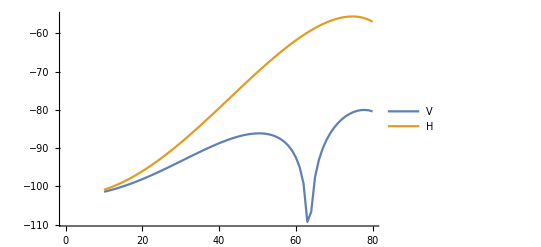

```mathematica
ListPlot[{inv, inh}, Joined->True, PlotLegends->{"V", "H"}]
```

```mathematica
inv
```

{{10.01,-101.397},{15.01,-99.9713},{20.01,-98.0869},{25.01,-95.8549},{30.01,-93.4191},{35.01,-90.9601},{40.01,-88.7038},{45.01,-86.9464},{50.01,-86.1225},{55.01,-87.0483},{60.01,-92.3829},{65.01,-97.5812},{70.01,-84.5992},{75.01,-80.5573},{80.01,-80.3655}}

## Step 5 (a). Load plotting program and Data from dry snow-----Fig 8.10 (a)

```mathematica
dav={{{10,-2},ErrorBar[0.5]},{{20,-5.},ErrorBar[0.5]},{{30,-5.7},ErrorBar[0.5]},{{40,-6.3},ErrorBar[0.5]},{{50,-7.0},ErrorBar[0.5]},{{60,-7.5},ErrorBar[0.5]},{{70,-9.1},ErrorBar[0.5]},{{80,-14},ErrorBar[0.5]}};

dah={{{10,-2},ErrorBar[0.5]},{{20,-5.},ErrorBar[0.5]},{{30,-5.7},ErrorBar[0.5]},{{40,-6.3},ErrorBar[0.5]},{{50,-7.0},ErrorBar[0.5]},{{60,-7.5},ErrorBar[0.5]},{{70,-9.1},ErrorBar[0.5]},{{80,-14},ErrorBar[0.5]}};

g1=Graphics[MultipleListPlot[vv,hh,dav,dah,
	PlotStyle->{Dashing[{0.03,0.03}],Dashing[{0.01,0.01}],{Hue[.85]},{Hue[.3]},{Hue[0.5]},{Hue[0.1]}},
	AspectRatio->1,
	PlotLegend->{FontForm["vv",{"Arial",14}],FontForm["hh",{"Arial",14}],FontForm["dav",{"Arial",14}],FontForm["dah",{"Arial",14}],FontForm["vIEM",{"Arial",14}],FontForm["hIEM",{"Arial",14}]},
	PlotRange->{-20,5},DisplayFunction->Identity,
	SymbolShape->{MakeSymbol[RegularPolygon[5,0]],MakeSymbol[RegularPolygon[4,0]],PlotSymbol[Star,5],PlotSymbol[Diamond,5],MakeSymbol[RegularPolygon[3,0]],MakeSymbol[RegularPolygon[6,0]]},
		PlotLabel->FontForm["Scattering Coefficient",{"Arial",16}],Frame->True,Axes->False,
	PlotJoined->{True,True,False,False,True,True},FrameLabel->{FontForm["θ",{"Arial",18}],FontForm["σ^0",{"Arial",18}]},Background->GrayLevel[0.998],DefaultFont->14,GridLines->Automatic,RotateLabel->False]];
```

## Step 6 (a). Show plots --data from p. 879--vol.2 17 GHz-----Fig 8.10 (a)

```mathematica
Show[g1,DisplayFunction->$DisplayFunction];
```

```mathematica
Fig 8.10 (a)
```

## Step 4 (b). Compute backscattering from a Rayleigh layer with irregular boundaries----Fig 8.10 (b) using wet snow --data from p.877-----vol.2

```mathematica
fr=17;  al=0.17;tau=2.5; phs=180;
theta=thetas;er=1.7-I 0.005;erb=5;sig1=.1;sig2=0.5; L1=1.2; L2=20.0;sp=1;

start=10.010;end=70.01;step=5;

outp=Table[Rlay[fr,al,tau,theta,thetas,phs,er,erb/er,sig1,sig2,L1,L2,sp],{thetas,start,end,step}];
vv=Map[{#[[1]],#[[2]]}&,outp];
hh=Map[{#[[1]],#[[3]]}&,outp];
vov=Map[{#[[1]],#[[4]]}&,outp];
voh=Map[{#[[1]],#[[5]]}&,outp];
inv=Map[{#[[1]],#[[6]]}&,outp];
inh=Map[{#[[1]],#[[7]]}&,outp];
stv=Map[{#[[1]],#[[8]]}&,outp];
sth=Map[{#[[1]],#[[9]]}&,outp];
sbv=Map[{#[[1]],#[[10]]}&,outp];
sbh=Map[{#[[1]],#[[11]]}&,outp];

Needs["Statistics`DataManipulation`"];
Needs["Graphics`MultipleListPlot`"];

Print[TableForm[{vv,vov,inv,stv,sbv},TableHeadings->{{"VV σ^0"},{"Layer"}}]];
Print[TableForm[{hh,voh,inh,sth,sbh},TableHeadings->{{"HH σ^0"},{"Layer"}}]];
```

| Layer |  |  |  |  |  |  |  |  |  |  |  | 
VV σ^0 | 10.01
-7.86568 | 15.01
-8.61294 | 20.01
-9.00114 | 25.01
-9.27299 | 30.01
-9.51834 | 35.01
-9.77532 | 40.01
-10.0651 | 45.01
-10.4046 | 50.01
-10.8128 | 55.01
-11.3162 | 60.01
-11.9569 | 65.01
-12.8069 | 70.01
-13.9999
 | 10.01
-9.18478 | 15.01
-9.25834 | 20.01
-9.36326 | 25.01
-9.50174 | 30.01
-9.67696 | 35.01
-9.89354 | 40.01
-10.1582 | 45.01
-10.4808 | 50.01
-10.8768 | 55.01
-11.3705 | 60.01
-12.0027 | 65.01
-12.8447 | 70.01
-14.0297
 | 10.01
-130.71 | 15.01
-129.506 | 20.01
-127.935 | 25.01
-126.109 | 30.01
-124.172 | 35.01
-122.301 | 40.01
-120.71 | 45.01
-119.663 | 50.01
-119.501 | 55.01
-120.737 | 60.01
-124.407 | 65.01
-134.819 | 70.01
-134.27
 | 10.01
-13.8109 | 15.01
-17.3251 | 20.01
-20.0727 | 25.01
-22.2629 | 30.01
-24.0532 | 35.01
-25.5573 | 40.01
-26.8653 | 45.01
-28.0565 | 50.01
-29.2099 | 55.01
-30.4143 | 60.01
-31.7815 | 65.01
-33.4653 | 70.01
-35.6823
 | 10.01
-29.0779 | 15.01
-33.0825 | 20.01
-36.2994 | 25.01
-38.9702 | 30.01
-41.2702 | 35.01
-43.3245 | 40.01
-45.2267 | 45.01
-47.0516 | 50.01
-48.862 | 55.01
-50.7135 | 60.01
-52.6601 | 65.01
-54.7653 | 70.01
-57.1299

| Layer |  |  |  |  |  |  |  |  |  |  |  | 
HH σ^0 | 10.01
-7.89877 | 15.01
-8.6753 | 20.01
-9.09551 | 25.01
-9.40575 | 30.01
-9.69953 | 35.01
-10.0184 | 40.01
-10.3872 | 45.01
-10.8275 | 50.01
-11.3645 | 55.01
-12.0327 | 60.01
-12.8855 | 65.01
-14.0102 | 70.01
-15.5604
 | 10.01
-9.19938 | 15.01
-9.29176 | 20.01
-9.42416 | 25.01
-9.60004 | 30.01
-9.82437 | 35.01
-10.1042 | 40.01
-10.4496 | 45.01
-10.8751 | 50.01
-11.4023 | 55.01
-12.0641 | 60.01
-12.9126 | 65.01
-14.0351 | 70.01
-15.5862
 | 10.01
-130.172 | 15.01
-128.288 | 20.01
-125.746 | 25.01
-122.639 | 30.01
-119.082 | 35.01
-115.207 | 40.01
-111.166 | 45.01
-107.12 | 50.01
-103.243 | 55.01
-99.7137 | 60.01
-96.7178 | 65.01
-94.4575 | 70.01
-93.1758
 | 10.01
-13.8898 | 15.01
-17.5606 | 20.01
-20.5544 | 25.01
-23.0653 | 30.01
-25.2313 | 35.01
-27.1457 | 40.01
-28.876 | 45.01
-30.4764 | 50.01
-31.9947 | 55.01
-33.4752 | 60.01
-34.9527 | 65.01
-36.431 | 70.01
-37.8445
 | 10.01
-29.3963 | 15.01
-33.8059 | 20.01
-37.5891 | 25.01
-40.9862 | 30.01
-44.1706 | 35.01
-47.2634 | 40.01
-50.3507 | 45.01
-53.4941 | 50.01
-56.7343 | 55.01
-60.0926 | 60.01
-63.5752 | 65.01
-67.1871 | 70.01
-70.9734

Null^18

## Step 5 (b). Load plotting program and Data from wet snow----Fig 8.10 (b)

```mathematica
dav={{{10,-8},ErrorBar[0.5]},{{20,-9.},ErrorBar[0.5]},{{30,-9.5},ErrorBar[0.5]},{{40,-10},ErrorBar[0.5]},{{50,-10.7},ErrorBar[0.5]},{{60,-12.0},ErrorBar[0.5]},{{70,-14.5},ErrorBar[0.5]}};

dah={{{10,-8},ErrorBar[0.5]},{{20,-9.},ErrorBar[0.5]},{{30,-9.5},ErrorBar[0.5]},{{40,-10},ErrorBar[0.5]},{{50,-10.7},ErrorBar[0.5]},{{60,-12.0},ErrorBar[0.5]},{{70,-14.5},ErrorBar[0.5]}};

g1=Graphics[MultipleListPlot[vv,hh,dav,dah,
	PlotStyle->{Dashing[{0.03,0.03}],Dashing[{0.01,0.01}],{Hue[.85]},{Hue[.3]},{Hue[0.5]},{Hue[0.1]}},
	AspectRatio->1,
	PlotLegend->{FontForm["vv",{"Arial",14}],FontForm["hh",{"Arial",14}],FontForm["dav",{"Arial",14}],FontForm["dah",{"Arial",14}],FontForm["vIEM",{"Arial",14}],FontForm["hIEM",{"Arial",14}]},
	PlotRange->{-20,-5},DisplayFunction->Identity,
	SymbolShape->{MakeSymbol[RegularPolygon[5,0]],MakeSymbol[RegularPolygon[4,0]],PlotSymbol[Star,5],PlotSymbol[Diamond,5],MakeSymbol[RegularPolygon[3,0]],MakeSymbol[RegularPolygon[6,0]]},
		PlotLabel->FontForm["Scattering Coefficient",{"Arial",16}],Frame->True,Axes->False,
	PlotJoined->{True,True,False,False,True,True},FrameLabel->{FontForm["θ",{"Arial",18}],FontForm["σ^0",{"Arial",18}]},Background->GrayLevel[0.998],DefaultFont->14,GridLines->Automatic,RotateLabel->False]];
```

Null^3

## Step 6 (b). Show plots ---data from p. 877--vol.2 17 GHz-----Fig 8.10 (b)

```mathematica
Show[g1,DisplayFunction->$DisplayFunction];
```

```mathematica
Fig 8.10 (b)
```